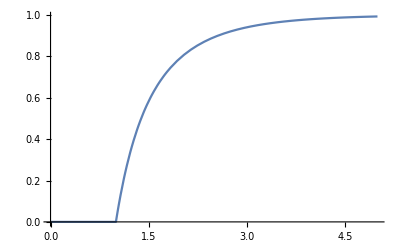

```mathematica
Plot[FindRoot[Rinf==1-Exp[-Ro*Rinf],{Rinf,1}][[1,2]],{Ro,0,5}]
```

#### Flu

```mathematica
FindRoot[Rinf==1-Exp[-1.2*Rinf],{Rinf,1}]
```

{Rinf→0.313698}

```mathematica
FindRoot[Rinf==1-Exp[-3*Rinf],{Rinf,1}]
```

{Rinf→0.94048}

```mathematica
1-1/1.2
```

0.166667

```mathematica
1-1/3.
```

0.666667

#### Rubella

```mathematica
FindRoot[Rinf==1-Exp[-6*Rinf],{Rinf,1}]
```

{Rinf→0.997484}

```mathematica
FindRoot[Rinf==1-Exp[-8*Rinf],{Rinf,1}]
```

{Rinf→0.999664}

```mathematica
1-1/6.
```

0.833333

```mathematica
1-1/8.
```

0.875

#### Measles

```mathematica
FindRoot[Rinf==1-Exp[-16*Rinf],{Rinf,1}]
```

{Rinf→1.}

```mathematica
1-1/16.
```

0.9375

```mathematica
FindRoot[Rinf==1-Exp[-18*Rinf],{Rinf,1}]
```

{Rinf→1.}

```mathematica
1-1/18.
```

0.944444

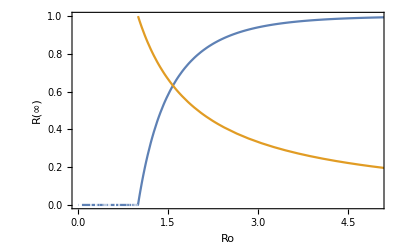

```mathematica
Plot[{FindRoot[Rinf==1-Exp[-Ro*Rinf],{Rinf,1}][[1,2]],1/Ro},{Ro,0,10},Frame->True, FrameLabel->{"Ro","R(∞)"},PlotRange->{{0,5},{0,1}}]
```

## Runge-Kutta

```mathematica
NDSolve[{r'[t]==0.2*(1-s[0]*Exp[-18*r[t]]-r[t]),r[0]==0,i[0]==0.0001,s[0]==0.9999,r,r[t]+i[t]+s[0]==1},{r[t],i[t],s[t]},{t,0,30}]
```

NDSolve::deqn: Equation or list of equations expected instead of s[t]≥0 in the first argument {r'[t]==0.2 (1-r[t]-ⅇ^(-18 r[«1»]) s[0]),r[0]==0,i[0]==0.0001,s[0]==0.9999,s[t]≥0,r[t]≥0,i[t]>0,i[t]+r[t]+s[0]==1}.

NDSolve[{r'[t]==0.2 (1-r[t]-ⅇ^(-18 r[t]) s[0]),r[0]==0,i[0]==0.0001,s[0]==0.9999,s[t]≥0,r[t]≥0,i[t]>0,i[t]+r[t]+s[0]==1},{r[t],i[t],s[t]},{t,0,30}]

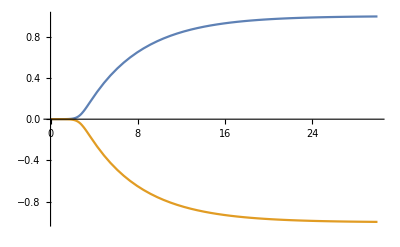

```mathematica
Plot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,30}]
```